## Initialization

```mathematica
SetDirectory[NotebookDirectory[]]
Get["SuperDataAnalysis.m"]
```

D:\Libraries\_Git Public\Wolfram-Mathematica

### Working directory

```mathematica
SetWorkingDirectory[]
```

Working directory set to: D:\Libraries\_Git Public\Wolfram-Mathematica\

### Dataset

```mathematica
datasetFile=FileNameJoin[{NotebookDirectory[],"Nb_DB_13_datasets.wl"}]
```

D:\Libraries\_Git Public\Wolfram-Mathematica\Nb_DB_13_datasets.wl

```mathematica
Get[datasetFile];
```

#### Critical current I_C as a function of T

```mathematica
IonicGatingIcVTemp
```

Dataset[<>]

#### Retrapping current I_R as a function of T

```mathematica
IonicGatingIrVTemp
```

Dataset[<>]

#### Critical current I_C as a function of T, repetition measurements

```mathematica
IonicGatingIcVTempRepetitions
```

Dataset[<>]

### Take quarter functions

```mathematica
TakeFirstQuarter[list_]:=list[[1;;Floor[Length[list]/4]]]
TakeSecondQuarter[list_]:=list[[Floor[Length[list]/4]+1;;2*Floor[Length[list]/4]]]
TakeThirdQuarter[list_]:=list[[2*Floor[Length[list]/4]+1;;3*Floor[Length[list]/4]]]
TakeFourthQuarter[list_]:=list[[3*Floor[Length[list]/4]+1;;Length[list]]]
```

### Determining I_C and I_R

#### I_C up and down

```mathematica
Clear[ShowIcStandard,FindIcStandard];
ShowIcStandard[threshold_:0.001]:=
Module[
{listX=S2Split[TakeColumn[1]], listY=S2Split[TakeColumn[5]]},
(*Join the up and (rectified) down sweep sweep*)
listX = Join[Map[TakeSecondQuarter,listX],-Map[TakeFourthQuarter,listX]];
listY = Join[Map[TakeSecondQuarter,listY],-Map[TakeFourthQuarter,listY]];

ShowFindSlopeArray[listX,listY,threshold,1,-1]
]

FindIcStandard[threshold_:0.001]:=
Module[
{listX=S2Split[TakeColumn[1]], listY=S2Split[TakeColumn[5]],meanTemperature},
(*Take the average temperature of every sweep, then duplicate the list since we take two quarters*)
meanTemperature = Map[Mean,S2Split[TakeColumn[4]]];
meanTemperature=Join[meanTemperature,meanTemperature];

(*Join the up and (rectified) down sweep sweep*)
listX = Join[Map[TakeSecondQuarter,listX],-Map[TakeFourthQuarter,listX]];
listY = Join[Map[TakeSecondQuarter,listY],-Map[TakeFourthQuarter,listY]];

(*Combine the average temperature of the sweep with the corrosponding Ic*)
Transpose[{meanTemperature,FindSlopeArray[listX,listY,threshold,1,-1]}]
]
```

#### I_R up and down

```mathematica
Clear[ShowIrStandard,FindIrStandard];
ShowIrStandard[threshold_:0.001]:=
Module[
{listX=S2Split[TakeColumn[1]], listY=S2Split[TakeColumn[5]]},
(*Join the up and (rectified) down sweep sweep*)
listX = Join[Map[-Reverse[TakeFirstQuarter[#]]&,listX],Map[Reverse[TakeThirdQuarter[#]]&,listX]];
listY = Join[Map[-Reverse[TakeFirstQuarter[#]]&,listY],Map[Reverse[TakeThirdQuarter[#]]&,listY]];

ShowFindSlopeArray[listX,listY,threshold,1,-1]
]

FindIrStandard[threshold_:0.001]:=
Module[
{listX=S2Split[TakeColumn[1]], listY=S2Split[TakeColumn[5]],meanTemperature,Ir},
(*Take the average temperature of every sweep, then duplicate the list since we take two quarters*)
meanTemperature = Map[Mean,S2Split[TakeColumn[4]]];
meanTemperature=Join[meanTemperature,meanTemperature];

(*Join the up and (rectified) down sweep sweep*)
listX = Join[Map[-Reverse[TakeFirstQuarter[#]]&,listX],Map[Reverse[TakeThirdQuarter[#]]&,listX]];
listY = Join[Map[-Reverse[TakeFirstQuarter[#]]&,listY],Map[Reverse[TakeThirdQuarter[#]]&,listY]];

Ir = FindSlopeArray[listX,listY,threshold,1,-1];
(*Ir=Map[#-3*&,Ir];*)
(*Combine the average temperature of the sweep with the corrosponding Ic*)
Transpose[{meanTemperature,Ir}]
]
```

## Measurement Example

### m006 V_Gate= 1 V, standard

```mathematica
LoadGlobalFile[]
```

Directory = D:\Libraries\_Google Drive SNS\PhD Pisa\Calculations, Data and Designs\Measurements\2020-09-01 NB DB 14\2020-10-30 
File name = m006

First row of selectedFile: {s1,s2,SWL,Sensor,1,[K],HP334xx,[V],time,[s],SMU,1,in,[A]}

Number of sweeps detected: 2

s1Length = 1202

s1Values = {-30.,-29.9,-29.8,-29.7,-29.6,-29.5,-29.4,-29.3,-29.2,-29.1,-29.,-28.9,-28.8,-28.7,-28.6,-28.5,-28.4,-28.3,-28.2,-28.1,-28.,-27.9,-27.8,-27.7,-27.6,-27.5,-27.4,-27.3,-27.2,-27.1,-27.,-26.9,-26.8,-26.7,-26.6,-26.5,-26.4,-26.3,-26.2,-26.1,-26.,-25.9,-25.8,-25.7,-25.6,-25.5,-25.4,-25.3,-25.2,-25.1,-25.,-24.9,-24.8,-24.7,-24.6,-24.5,-24.4,-24.3,-24.2,-24.1,-24.,-23.9,-23.8,-23.7,-23.6,-23.5,-23.4,-23.3,-23.2,-23.1,-23.,-22.9,-22.8,-22.7,-22.6,-22.5,-22.4,-22.3,-22.2,-22.1,-22.,-21.9,-21.8,-21.7,-21.6,-21.5,-21.4,-21.3,-21.2,-21.1,-21.,-20.9,-20.8,-20.7,-20.6,-20.5,-20.4,-20.3,-20.2,-20.1,-20.,-19.9,-19.8,-19.7,-19.6,-19.5,-19.4,-19.3,-19.2,-19.1,-19.,-18.9,-18.8,-18.7,-18.6,-18.5,-18.4,-18.3,-18.2,-18.1,-18.,-17.9,-17.8,-17.7,-17.6,-17.5,-17.4,-17.3,-17.2,-17.1,-17.,-16.9,-16.8,-16.7,-16.6,-16.5,-16.4,-16.3,-16.2,-16.1,-16.,-15.9,-15.8,-15.7,-15.6,-15.5,-15.4,-15.3,-15.2,-15.1,-15.,-14.9,-14.8,-14.7,-14.6,-14.5,-14.4,-14.3,-14.2,-14.1,-14.,-13.9,-13.8,-13.7,-13.6,-13.5,-13.4,-13.3,-13.2,-13.1,-13.,-12.9,-12.8,-12.7,-12.6,-12.5,-12.4,-12.3,-12.2,-12.1,-12.,-11.9,-11.8,-11.7,-11.6,-11.5,-11.4,-11.3,-11.2,-11.1,-11.,-10.9,-10.8,-10.7,-10.6,-10.5,-10.4,-10.3,-10.2,-10.1,-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.,29.9,29.8,29.7,29.6,29.5,29.4,29.3,29.2,29.1,29.,28.9,28.8,28.7,28.6,28.5,28.4,28.3,28.2,28.1,28.,27.9,27.8,27.7,27.6,27.5,27.4,27.3,27.2,27.1,27.,26.9,26.8,26.7,26.6,26.5,26.4,26.3,26.2,26.1,26.,25.9,25.8,25.7,25.6,25.5,25.4,25.3,25.2,25.1,25.,24.9,24.8,24.7,24.6,24.5,24.4,24.3,24.2,24.1,24.,23.9,23.8,23.7,23.6,23.5,23.4,23.3,23.2,23.1,23.,22.9,22.8,22.7,22.6,22.5,22.4,22.3,22.2,22.1,22.,21.9,21.8,21.7,21.6,21.5,21.4,21.3,21.2,21.1,21.,20.9,20.8,20.7,20.6,20.5,20.4,20.3,20.2,20.1,20.,19.9,19.8,19.7,19.6,19.5,19.4,19.3,19.2,19.1,19.,18.9,18.8,18.7,18.6,18.5,18.4,18.3,18.2,18.1,18.,17.9,17.8,17.7,17.6,17.5,17.4,17.3,17.2,17.1,17.,16.9,16.8,16.7,16.6,16.5,16.4,16.3,16.2,16.1,16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5,13.4,13.3,13.2,13.1,13.,12.9,12.8,12.7,12.6,12.5,12.4,12.3,12.2,12.1,12.,11.9,11.8,11.7,11.6,11.5,11.4,11.3,11.2,11.1,11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.,8.9,8.8,8.7,8.6,8.5,8.4,8.3,8.2,8.1,8.,7.9,7.8,7.7,7.6,7.5,7.4,7.3,7.2,7.1,7.,6.9,6.8,6.7,6.6,6.5,6.4,6.3,6.2,6.1,6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.,-1.1,-1.2,-1.3,-1.4,-1.5,-1.6,-1.7,-1.8,-1.9,-2.,-2.1,-2.2,-2.3,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.,-3.1,-3.2,-3.3,-3.4,-3.5,-3.6,-3.7,-3.8,-3.9,-4.,-4.1,-4.2,-4.3,-4.4,-4.5,-4.6,-4.7,-4.8,-4.9,-5.,-5.1,-5.2,-5.3,-5.4,-5.5,-5.6,-5.7,-5.8,-5.9,-6.,-6.1,-6.2,-6.3,-6.4,-6.5,-6.6,-6.7,-6.8,-6.9,-7.,-7.1,-7.2,-7.3,-7.4,-7.5,-7.6,-7.7,-7.8,-7.9,-8.,-8.1,-8.2,-8.3,-8.4,-8.5,-8.6,-8.7,-8.8,-8.9,-9.,-9.1,-9.2,-9.3,-9.4,-9.5,-9.6,-9.7,-9.8,-9.9,-10.,-10.1,-10.2,-10.3,-10.4,-10.5,-10.6,-10.7,-10.8,-10.9,-11.,-11.1,-11.2,-11.3,-11.4,-11.5,-11.6,-11.7,-11.8,-11.9,-12.,-12.1,-12.2,-12.3,-12.4,-12.5,-12.6,-12.7,-12.8,-12.9,-13.,-13.1,-13.2,-13.3,-13.4,-13.5,-13.6,-13.7,-13.8,-13.9,-14.,-14.1,-14.2,-14.3,-14.4,-14.5,-14.6,-14.7,-14.8,-14.9,-15.,-15.1,-15.2,-15.3,-15.4,-15.5,-15.6,-15.7,-15.8,-15.9,-16.,-16.1,-16.2,-16.3,-16.4,-16.5,-16.6,-16.7,-16.8,-16.9,-17.,-17.1,-17.2,-17.3,-17.4,-17.5,-17.6,-17.7,-17.8,-17.9,-18.,-18.1,-18.2,-18.3,-18.4,-18.5,-18.6,-18.7,-18.8,-18.9,-19.,-19.1,-19.2,-19.3,-19.4,-19.5,-19.6,-19.7,-19.8,-19.9,-20.,-20.1,-20.2,-20.3,-20.4,-20.5,-20.6,-20.7,-20.8,-20.9,-21.,-21.1,-21.2,-21.3,-21.4,-21.5,-21.6,-21.7,-21.8,-21.9,-22.,-22.1,-22.2,-22.3,-22.4,-22.5,-22.6,-22.7,-22.8,-22.9,-23.,-23.1,-23.2,-23.3,-23.4,-23.5,-23.6,-23.7,-23.8,-23.9,-24.,-24.1,-24.2,-24.3,-24.4,-24.5,-24.6,-24.7,-24.8,-24.9,-25.,-25.1,-25.2,-25.3,-25.4,-25.5,-25.6,-25.7,-25.8,-25.9,-26.,-26.1,-26.2,-26.3,-26.4,-26.5,-26.6,-26.7,-26.8,-26.9,-27.,-27.1,-27.2,-27.3,-27.4,-27.5,-27.6,-27.7,-27.8,-27.9,-28.,-28.1,-28.2,-28.3,-28.4,-28.5,-28.6,-28.7,-28.8,-28.9,-29.,-29.1,-29.2,-29.3,-29.4,-29.5,-29.6,-29.7,-29.8,-29.9,-30.}

s2Length = 31

s2Values = {6.,5.9,5.8,5.7,5.6,5.5,5.4,5.3,5.2,5.1,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.}

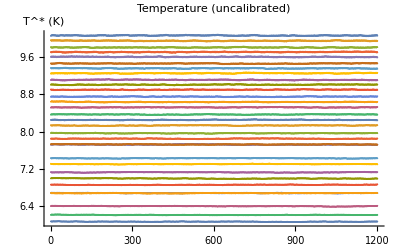

```mathematica
ListPlot[S2Split[TakeColumn[4]],PlotLabel->"Temperature (uncalibrated)",AxesLabel->{"","T^* (K)"}]
```

#### Show I_C

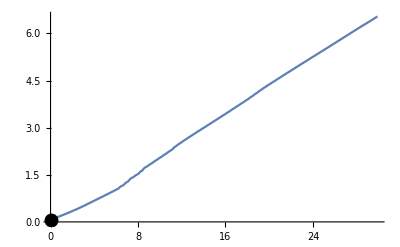
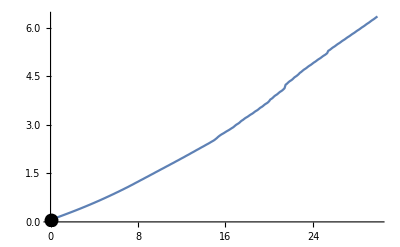
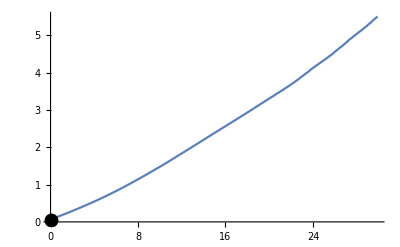
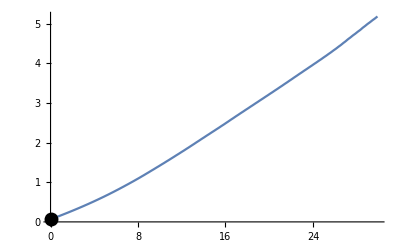
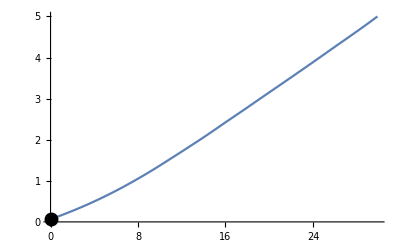
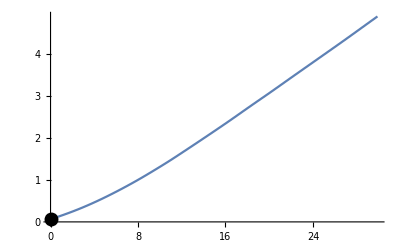
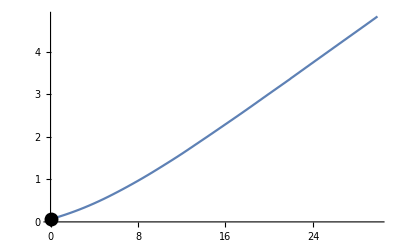
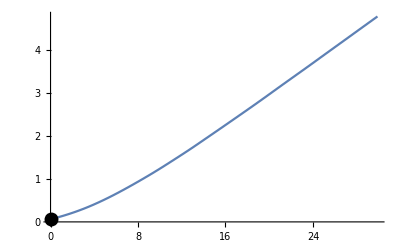
{{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{3,0.2,-Graphics-},{7,0.6,-Graphics-},{13,1.2,-Graphics-},{23,2.2,-Graphics-},{33,3.2,-Graphics-},{43,4.2,-Graphics-},{56,5.5,-Graphics-},{68,6.7,-Graphics-},{84,8.3,-Graphics-},{105,10.4,-Graphics-},{112,11.1,-Graphics-},{143,14.2,-Graphics-},{122,12.1,-Graphics-},{171,17.,-Graphics-},{212,21.1,-Graphics-},{228,22.7,-Graphics-},{239,23.8,-Graphics-},{274,27.3,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{1,-0.1,-Graphics-},{5,0.3,-Graphics-},{9,0.7,-Graphics-},{14,1.2,-Graphics-},{25,2.3,-Graphics-},{34,3.2,-Graphics-},{43,4.1,-Graphics-},{57,5.5,-Graphics-},{69,6.7,-Graphics-},{84,8.2,-Graphics-},{108,10.6,-Graphics-},{122,12.,-Graphics-},{136,13.4,-Graphics-},{126,12.4,-Graphics-},{192,19.,-Graphics-},{206,20.4,-Graphics-},{230,22.8,-Graphics-},{198,19.6,-Graphics-},{257,25.5,-Graphics-},{290,28.8,-Graphics-},{300,29.8,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-}}

```mathematica
ShowIcStandard[]
```

#### Find I_C

```mathematica
FindIcStandard[]
```

{{10.0606,0.},{9.94761,0.},{9.8041,0.},{9.70592,0.},{9.6019,0.},{9.45981,0.},{9.35621,0.},{9.25166,0.},{9.10909,0.2},{9.00639,0.6},{8.89817,1.2},{8.7498,2.2},{8.63487,3.2},{8.51968,4.2},{8.36719,5.5},{8.2508,6.7},{8.1313,8.3},{7.96485,10.4},{7.84808,11.1},{7.72119,14.2},{7.72505,12.1},{7.42739,17.},{7.30262,21.1},{7.12649,22.7},{6.99429,23.8},{6.85862,27.3},{6.6818,-1},{6.67938,-1},{6.40075,-1},{6.21304,-1},{6.0688,-1},{10.0606,-0.1},{9.94761,-0.1},{9.8041,-0.1},{9.70592,-0.1},{9.6019,-0.1},{9.45981,-0.1},{9.35621,-0.1},{9.25166,-0.1},{9.10909,0.3},{9.00639,0.7},{8.89817,1.2},{8.7498,2.3},{8.63487,3.2},{8.51968,4.1},{8.36719,5.5},{8.2508,6.7},{8.1313,8.2},{7.96485,10.6},{7.84808,12.},{7.72119,13.4},{7.72505,12.4},{7.42739,19.},{7.30262,20.4},{7.12649,22.8},{6.99429,19.6},{6.85862,25.5},{6.6818,28.8},{6.67938,29.8},{6.40075,-1},{6.21304,-1},{6.0688,-1}}

```mathematica
IonicGatingIcVTemp=Insert[IonicGatingIcVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m006","VGate"->1,"IcvTemp"->FindIcStandard[]|>,1];
```

#### Show I_R

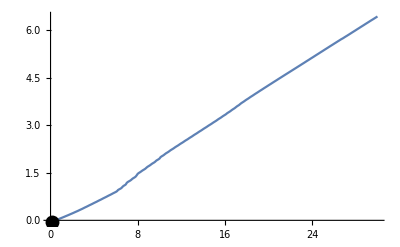
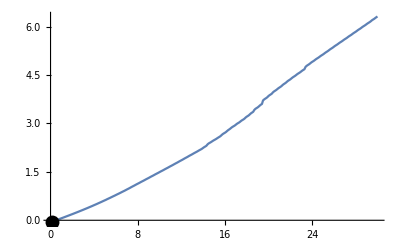
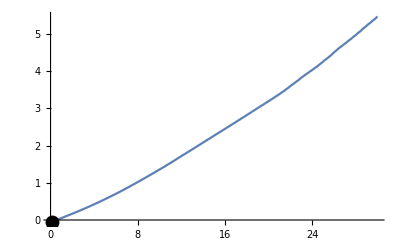
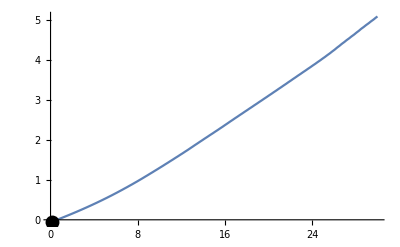
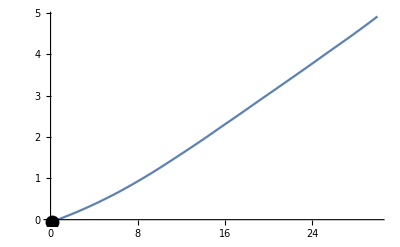
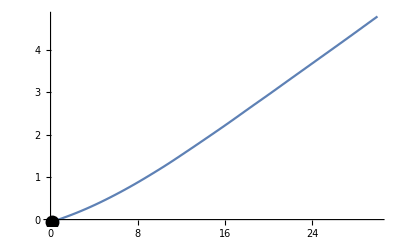
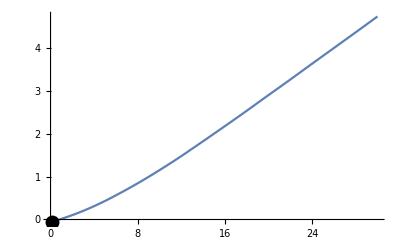
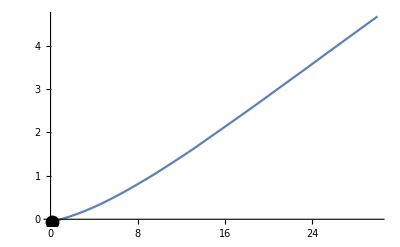
{{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{1,0.1,-Graphics-},{2,0.2,-Graphics-},{6,0.6,-Graphics-},{12,1.2,-Graphics-},{22,2.2,-Graphics-},{32,3.2,-Graphics-},{40,4.,-Graphics-},{49,4.9,-Graphics-},{57,5.7,-Graphics-},{64,6.4,-Graphics-},{73,7.3,-Graphics-},{79,7.9,-Graphics-},{85,8.5,-Graphics-},{85,8.5,-Graphics-},{98,9.8,-Graphics-},{103,10.3,-Graphics-},{109,10.9,-Graphics-},{114,11.4,-Graphics-},{118,11.8,-Graphics-},{123,12.3,-Graphics-},{123,12.3,-Graphics-},{130,13.,-Graphics-},{134,13.4,-Graphics-},{-1,-1,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{1,0.2,-Graphics-},{2,0.3,-Graphics-},{6,0.7,-Graphics-},{11,1.2,-Graphics-},{22,2.3,-Graphics-},{31,3.2,-Graphics-},{39,4.,-Graphics-},{49,5.,-Graphics-},{56,5.7,-Graphics-},{63,6.4,-Graphics-},{71,7.2,-Graphics-},{77,7.8,-Graphics-},{84,8.5,-Graphics-},{84,8.5,-Graphics-},{96,9.7,-Graphics-},{101,10.2,-Graphics-},{110,11.1,-Graphics-},{112,11.3,-Graphics-},{116,11.7,-Graphics-},{122,12.3,-Graphics-},{122,12.3,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-},{-1,-1,-Graphics-}}

```mathematica
ShowIrStandard[]
```

#### Find I_R

```mathematica
FindIrStandard[]
```

{{10.0606,0.1},{9.94761,0.1},{9.8041,0.1},{9.70592,0.1},{9.6019,0.1},{9.45981,0.1},{9.35621,0.1},{9.25166,0.1},{9.10909,0.2},{9.00639,0.6},{8.89817,1.2},{8.7498,2.2},{8.63487,3.2},{8.51968,4.},{8.36719,4.9},{8.2508,5.7},{8.1313,6.4},{7.96485,7.3},{7.84808,7.9},{7.72119,8.5},{7.72505,8.5},{7.42739,9.8},{7.30262,10.3},{7.12649,10.9},{6.99429,11.4},{6.85862,11.8},{6.6818,12.3},{6.67938,12.3},{6.40075,13.},{6.21304,13.4},{6.0688,-1},{10.0606,0.2},{9.94761,0.2},{9.8041,0.2},{9.70592,0.2},{9.6019,0.2},{9.45981,0.2},{9.35621,0.2},{9.25166,0.2},{9.10909,0.3},{9.00639,0.7},{8.89817,1.2},{8.7498,2.3},{8.63487,3.2},{8.51968,4.},{8.36719,5.},{8.2508,5.7},{8.1313,6.4},{7.96485,7.2},{7.84808,7.8},{7.72119,8.5},{7.72505,8.5},{7.42739,9.7},{7.30262,10.2},{7.12649,11.1},{6.99429,11.3},{6.85862,11.7},{6.6818,12.3},{6.67938,12.3},{6.40075,-1},{6.21304,-1},{6.0688,-1}}

```mathematica
IonicGatingIrVTemp=Insert[IonicGatingIrVTemp,<|"Device"->"Nb DB 14 dev C","Measurement"->"m006","VGate"->1,"IrvTemp"->FindIrStandard[]|>,1];
```

## Plots

### I_C All standard measurements

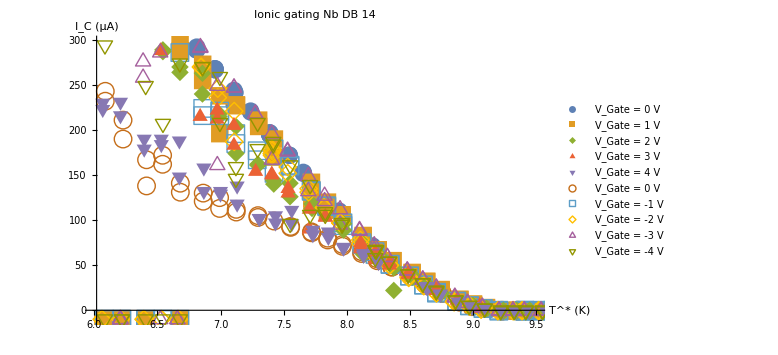

```mathematica
Module[{dataset, legend},
dataset = IonicGatingIcVTemp[SortBy[#Measurement&]];

legend=Normal[dataset[All,"VGate"]];
legend=Map["V_Gate = "<>ToString[#]<>" V"&,legend];
ListPlot[dataset[All,"IcvTemp"],PlotRange->{{6,9.5},Automatic},PlotLegends->legend,AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14",ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

#### I_R

```mathematica
IonicGatingIrVTemp
```

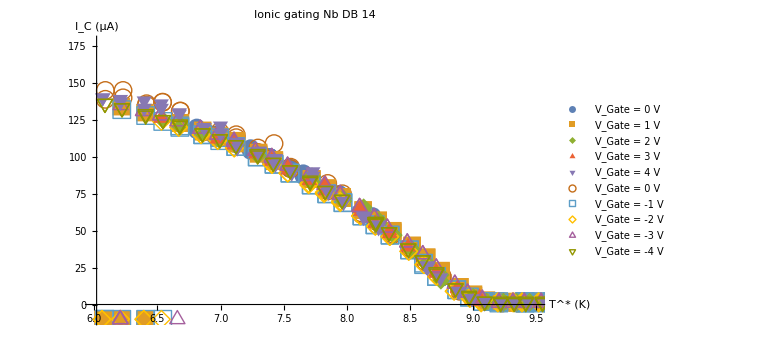

```mathematica
Module[{dataset, legend},
dataset = IonicGatingIrVTemp[SortBy[#Measurement&]];

legend=Normal[dataset[All,"VGate"]];
legend=Map["V_Gate = "<>ToString[#]<>" V"&,legend];
ListPlot[dataset[All,"IrvTemp"],PlotRange->{{6,9.5},Automatic},PlotLegends->legend,AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14",ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

### I_C compared to I_R

```mathematica
IonicGatingIcVTemp[All,#Measurement&]
```

Dataset[<>]

#### m006 (1 V)

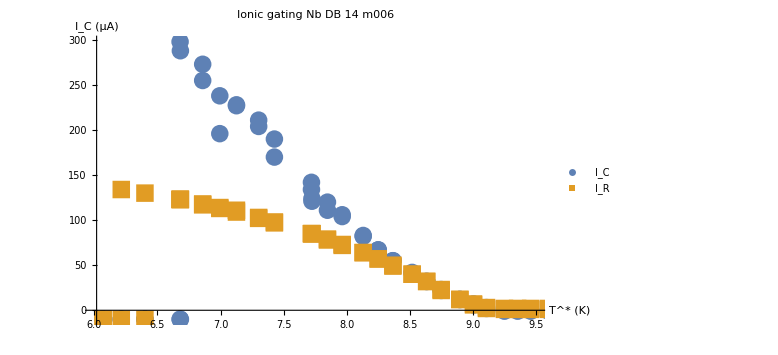

```mathematica
Module[{data, measurement="m006"},
data={Normal[IonicGatingIcVTemp[Select[#Measurement==measurement&]][1,#IcvTemp&]],Normal[IonicGatingIrVTemp[Select[#Measurement==measurement&]][1,#IrvTemp&]]};
ListPlot[data,PlotRange->{{6,9.5},Automatic},PlotLegends->{"I_C","I_R"},AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14 "<>measurement,ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

### Repetitions

```mathematica
Module[{dataset, legend},
dataset = IonicGatingIcVTempRepetitions[SortBy[#Measurement&]];

legend=Normal[dataset[All,"VGate"]];
legend=Map["V_Gate = "<>ToString[#]<>" V"&,legend];
ListPlot[dataset[All,"IcvTemp"],PlotRange->{{6,9.5},Automatic},PlotLegends->legend,AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14",ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

## I_C, Bardeen’s fit

### Bardeen’s fit data prep

```mathematica
Module[{data, measurement="m003"},
data={Normal[IonicGatingIcVTemp[Select[#Measurement==measurement&]][1,#IcvTemp&]],Normal[IonicGatingIrVTemp[Select[#Measurement==measurement&]][1,#IrvTemp&]]};
ListPlot[data,PlotRange->{{6,9.5},Automatic},PlotLegends->{"I_C","I_R"},AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14 "<>measurement,ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

```mathematica
Module[{data, dataset =IonicGatingIcVTemp },
data=IonicGatingIcVTemp[Select[#Measurement=="m003"||#Measurement == "m006"&]][SortBy[#Measurement&]];
data={
Normal[data[[1]][#IcvTemp&]],
Normal[data[[2]][#IcvTemp&]]
};

ListPlot[data,PlotRange->{{6,9.5},Automatic},PlotLegends->{"I_C","I_R"},AxesLabel->{"T^* (K)","I_C (µA)"},PlotLabel->"Ionic gating Nb DB 14 ",ImageSize->Large,PlotMarkers->{Automatic,18}]
]
```

-Graphics-

```mathematica
Module[{data1,data2, dataset =IonicGatingIcVTemp },
data1=Normal[IonicGatingIcVTemp[Select[#Measurement == "m003"&]][[1]][#IcvTemp&]];

data2=Normal[IonicGatingIcVTemp[Select[#Measurement == "m006"&]][[1]][#IcvTemp&]];
data2=Select[data2,#[[1]]>8&];

Join[data1,data2]//ListPlot
]
```

-Graphics-

### Bardeen’s function I_c fit

```mathematica
Clear[IcBardeen]
IcBardeen[IC0_,Tc_,T_]:=Re[IC0*(1-(T/Tc)^2)^(3/2)]
```

#### ref plot

```mathematica
fitBardeen=Module[{data1,data2,data, dataset =IonicGatingIcVTemp ,Tc=9.1},

data1=Normal[IonicGatingIcVTemp[Select[#Measurement == "m003"&]][[1]][#IcvTemp&]];
data2=Normal[IonicGatingIcVTemp[Select[#Measurement == "m006"&]][[1]][#IcvTemp&]];
data2=Select[data2,#[[1]]>8&];

data=Join[data1,data2];
data=Select[data,#[[2]]>0&];

NonlinearModelFit[data,IcBardeen[Ic0,Tc,T],{Ic0},T]
]

Show[{
Module[{data1,data2,data, dataset =IonicGatingIcVTemp, Ir},
dataset = IVsDataset[Select[#VGate==VGate&]];

data1=Normal[IonicGatingIcVTemp[Select[#Measurement == "m003"&]][[1]][#IcvTemp&]];
data2=Normal[IonicGatingIcVTemp[Select[#Measurement == "m006"&]][[1]][#IcvTemp&]];
data2=Select[data2,#[[1]]>8&];

data=Join[data1,data2];
data=Select[data,#[[2]]>0&];

Ir=Normal[IonicGatingIrVTemp[Select[#Measurement == "m006"&]][[1]][#IrvTemp&]];

ListPlot[{data,Ir},PlotRange->{{6,10},{0,350}},AxesLabel->{"T (K)","I_C (µA)"},PlotLabel->"Nb 14",ImageSize->Large,PlotMarkers->{Automatic,14},PlotLegends->{"I_C","I_R"}]
],
Plot[fitBardeen[T],{T,6,10},PlotRange->Full]
}]
```

FittedModel[985.67 Re[(1-0.0120758 T^2)^(3/2)]]

-Graphics-

## I_R fit

### fit

```mathematica
Module[{data,f},
data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];

Fit[data,{1,x,x^2},x]
]
```

628.898-97.374 x+3.33233 x^2

```mathematica
Module[{data,f},
data=IonicGatingIrVTemp[Select[#Measurement == "m006"&]];
data=Normal[data[[1]][#IrvTemp&]];
data=Select[data,#[[2]]>0&];
data=Select[data,#[[1]]<9&];

f=Fit[data,{1,x,x^2},x];
Show[{
Plot[f,{x,6,9.5}],
ListPlot[data]
}]
]
```

-Graphics-